```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
```

```mathematica
plin=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"..","data","pk_fid.dat"}]]];
```

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
perm1234=Permutations[{q1,q2,q3,q4}];

Clear[Fn,Gn,n,m,k1,k2,k3];
Fn[n_,v_]:=Fn[n,v]=If[n==1,1,Sum[(Gn[m,v[[1;;m]]]/((2n+3)(n-1)))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]:=Gn[n,v]=If[n==1,1,Sum[(Gn[m,v[[1;;m]]]/((2n+3)(n-1)))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2s[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3s[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+(1/2)((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2);
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);

ClearAll[alfdot,befdot, dot]
alfdot[k1_,k2_]:=(k1+k2).k1/(k1.k1)/.Dot -> dot;
befdot[k1_,k2_]:=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2)/.Dot -> dot ;

dot[a_+b_,c_]:=dot[a,c]+dot[b,c]
dot[a_,b_+c_]:=dot[a,b]+dot[a,c]
dot[s_ a_,b_]/;FreeQ[s,dot]:=s dot[a,b]
dot[a_,s_ b_]/;FreeQ[s,dot]:=s dot[a,b]
```

```mathematica
F3m = F3s[q, -q, k]/.{al:> alfm,be:>befm}//Expand
```

8/63-(5 mag[0]^2)/(216 mag[k]^2)+(5 mag[k]^2)/(504 mag[k-q]^2)+mag[k-q]^2/(216 mag[k]^2)+(37 mag[0]^2)/(3024 mag[-q]^2)-mag[0]^4/(144 mag[k]^2 mag[-q]^2)-(5 mag[k]^2)/(3024 mag[-q]^2)-(5 mag[k]^4)/(1008 mag[k-q]^2 mag[-q]^2)+(17 mag[k-q]^2)/(1512 mag[-q]^2)+mag[k-q]^4/(72 mag[k]^2 mag[-q]^2)-(7 mag[-q]^2)/(432 mag[k]^2)-(5 mag[-q]^2)/(1008 mag[k-q]^2)+(37 mag[0]^2)/(3024 mag[q]^2)-mag[0]^4/(144 mag[k]^2 mag[q]^2)-(5 mag[k]^2)/(3024 mag[q]^2)+mag[k]^4/(252 mag[k-q]^2 mag[q]^2)-(47 mag[k-q]^2)/(3024 mag[q]^2)-mag[k-q]^4/(144 mag[k]^2 mag[q]^2)+mag[0]^4/(63 mag[-q]^2 mag[q]^2)-mag[0]^6/(216 mag[k]^2 mag[-q]^2 mag[q]^2)-(31 mag[k]^4)/(1512 mag[-q]^2 mag[q]^2)-mag[k]^6/(504 mag[k-q]^2 mag[-q]^2 mag[q]^2)+(11 mag[k]^2 mag[k-q]^2)/(504 mag[-q]^2 mag[q]^2)-(5 mag[k-q]^4)/(1008 mag[-q]^2 mag[q]^2)-mag[k-q]^6/(216 mag[k]^2 mag[-q]^2 mag[q]^2)-(107 mag[-q]^2)/(3024 mag[q]^2)+(5 mag[0]^2 mag[-q]^2)/(432 mag[k]^2 mag[q]^2)-(mag[k]^2 mag[-q]^2)/(504 mag[k-q]^2 mag[q]^2)+(5 mag[k-q]^2 mag[-q]^2)/(432 mag[k]^2 mag[q]^2)-(7 mag[q]^2)/(432 mag[k]^2)-mag[q]^2/(72 mag[k-q]^2)-(107 mag[q]^2)/(3024 mag[-q]^2)+(5 mag[0]^2 mag[q]^2)/(432 mag[k]^2 mag[-q]^2)+(mag[k]^2 mag[q]^2)/(144 mag[k-q]^2 mag[-q]^2)-(mag[k-q]^2 mag[q]^2)/(108 mag[k]^2 mag[-q]^2)+(mag[-q]^2 mag[q]^2)/(144 mag[k]^2 mag[k-q]^2)+(5 mag[k]^2)/(504 mag[k+q]^2)+mag[k]^4/(252 mag[-q]^2 mag[k+q]^2)-mag[-q]^2/(72 mag[k+q]^2)-(5 mag[k]^4)/(1008 mag[q]^2 mag[k+q]^2)-mag[k]^6/(504 mag[-q]^2 mag[q]^2 mag[k+q]^2)+(mag[k]^2 mag[-q]^2)/(144 mag[q]^2 mag[k+q]^2)-(5 mag[q]^2)/(1008 mag[k+q]^2)-(mag[k]^2 mag[q]^2)/(504 mag[-q]^2 mag[k+q]^2)+(mag[-q]^2 mag[q]^2)/(144 mag[k]^2 mag[k+q]^2)+mag[k+q]^2/(216 mag[k]^2)-(47 mag[k+q]^2)/(3024 mag[-q]^2)+(17 mag[k+q]^2)/(1512 mag[q]^2)+(11 mag[k]^2 mag[k+q]^2)/(504 mag[-q]^2 mag[q]^2)-(mag[-q]^2 mag[k+q]^2)/(108 mag[k]^2 mag[q]^2)+(5 mag[q]^2 mag[k+q]^2)/(432 mag[k]^2 mag[-q]^2)-mag[k+q]^4/(144 mag[k]^2 mag[-q]^2)+mag[k+q]^4/(72 mag[k]^2 mag[q]^2)-(5 mag[k+q]^4)/(1008 mag[-q]^2 mag[q]^2)-mag[k+q]^6/(216 mag[k]^2 mag[-q]^2 mag[q]^2)

```mathematica
F3m = F3m/.{ mag[0]:> 0, mag[-q] :> mag[q]}
```

85/1512+(5 mag[k]^2)/(336 mag[k-q]^2)+mag[k-q]^2/(144 mag[k]^2)-(31 mag[k]^4)/(1512 mag[q]^4)-mag[k]^6/(504 mag[k-q]^2 mag[q]^4)+(11 mag[k]^2 mag[k-q]^2)/(504 mag[q]^4)-(5 mag[k-q]^4)/(1008 mag[q]^4)-mag[k-q]^6/(216 mag[k]^2 mag[q]^4)-(5 mag[k]^2)/(1512 mag[q]^2)-mag[k]^4/(1008 mag[k-q]^2 mag[q]^2)-(13 mag[k-q]^2)/(3024 mag[q]^2)+mag[k-q]^4/(144 mag[k]^2 mag[q]^2)-(7 mag[q]^2)/(216 mag[k]^2)-(19 mag[q]^2)/(1008 mag[k-q]^2)+mag[q]^4/(144 mag[k]^2 mag[k-q]^2)+(5 mag[k]^2)/(336 mag[k+q]^2)-mag[k]^6/(504 mag[q]^4 mag[k+q]^2)-mag[k]^4/(1008 mag[q]^2 mag[k+q]^2)-(19 mag[q]^2)/(1008 mag[k+q]^2)+mag[q]^4/(144 mag[k]^2 mag[k+q]^2)+mag[k+q]^2/(144 mag[k]^2)+(11 mag[k]^2 mag[k+q]^2)/(504 mag[q]^4)-(13 mag[k+q]^2)/(3024 mag[q]^2)-(5 mag[k+q]^4)/(1008 mag[q]^4)+mag[k+q]^4/(144 mag[k]^2 mag[q]^2)-mag[k+q]^6/(216 mag[k]^2 mag[q]^4)

```mathematica
F2m = F2s[q, k-q]/.{al :> alfm, be:> befm}//Expand
```

5/14+(3 mag[k]^2)/(28 mag[k-q]^2)+(3 mag[k]^2)/(28 mag[q]^2)+mag[k]^4/(14 mag[k-q]^2 mag[q]^2)-(5 mag[k-q]^2)/(28 mag[q]^2)-(5 mag[q]^2)/(28 mag[k-q]^2)

```mathematica
kBinslin[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=(kmax-kmin)/(Nmax-1)//N;
result=Table[kmin +(i-1) Δ,{i,1,Nmax}];
result
];
```

```mathematica
(* Nmax log k bins, from kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=(1/(Nmax-1))Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

```mathematica
NmaxPlot=100;
NmaxFit=100;
kminPlot=10^-3;
kminFit=10^-3;
kmaxPlot=2.;
kmaxFit=0.6;
knPlot=kBins[NmaxPlot,kminPlot,kmaxPlot];
knFit=kBins[NmaxFit,kminFit,kmaxFit];
```

```mathematica
IntegerFit[Plin_,knFit_,imax_]:=Module[{MyPsmoothtab,MyFitFunctions,Parameters,nlm,Pinteger,errors,kuv0,kuv1,kuv2,kuv3,kuv4,kpeak1,kpeak2,kpeak3,kpeak4},
MyPsmoothtab = Table[{knFit⟦i⟧,Plin[knFit⟦i⟧]},{i,1,Length[knFit]}];
errors=Flatten[Table[{MyPsmoothtab⟦i,2⟧ 10^-6},{i,1,Length[knFit]}]];

kuv0 = Rationalize[0.0001];
kuv1=Rationalize[0.069];
kuv2=Rationalize[0.0082];
kuv3=Rationalize[0.0013];
kuv4=Rationalize[0.0000135];
kpeak1=Rationalize[-0.034];
kpeak2=Rationalize[-0.001];
kpeak3=Rationalize[-0.000076];
kpeak4=Rationalize[-0.0000156];


Parameters=Flatten[Table[{a1[i],a2[i],a3[i], a4[i]},{i,0,imax}]];
MyFitFunctions=Delete[Flatten[Join[{1/(1+k^2/kuv0)},Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)), 1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)), 1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]]],2];

nlm=LinearModelFit[MyPsmoothtab,MyFitFunctions,k,Weights->1/errors^2,IncludeConstantBasis->False]; 
Pinteger[k_]=nlm[k];
{Pinteger,nlm["BestFitParameters"], {kuv0, kuv1, kuv2, kuv3,kuv4, kpeak1, kpeak2, kpeak3, kpeak4}}
]
imax=3;
{Pinteger,coeflin, parset}=IntegerFit[plin,knFit,imax];
```

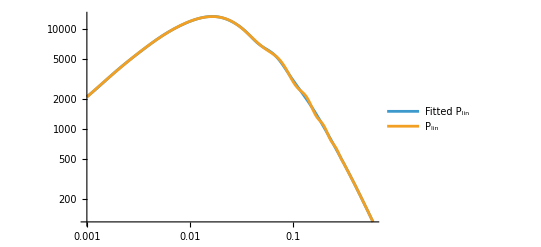

```mathematica
LogLogPlot[{Pinteger[q],plin[q]},{q,0.001,0.6},PlotLegends->{"Fitted P_lin", "P_lin"}]
```

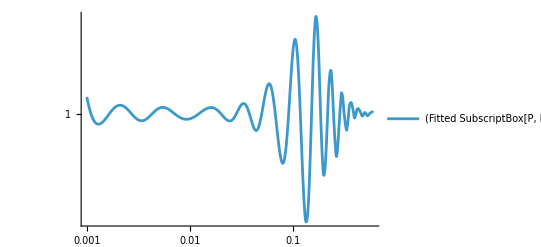

```mathematica
LogLogPlot[{Pinteger[q]/plin[q]},{q,0.001,0.6},PlotLegends->{"(Fitted SubscriptBox[P, lin])/P_lin"},PlotRange->All]
```

```mathematica
cosmo_coef = coeflin
```

{-10383.,1443.54,50570.3,-7330.55,461.381,1068.04,-63135.2,-41179.6,-783.879,-1506.16,22248.8,191370.,1127.49,7891.77,7433.93,-306078.}

```mathematica
Clear[MyFitFunctions]
MyFitFunctions[k_]:=Delete[Flatten[Join[{1/(1+k^2/kuv0)},Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)), 1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)), 1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]]],2];
```

```mathematica
Fitq = MyFitFunctions[q]
```

{1/(1+q^2/kuv0),(400 q^2)/(1+((-kpeak2+q^2)^2)/kuv2^2),1/((1+((-kpeak3+q^2)^2)/kuv3^2)^2),1/(1+((-kpeak4+q^2)^2)/kuv4^2),1/(1+((-kpeak1+q^2)^2)/kuv1^2),(400 q^2)/((1+((-kpeak2+q^2)^2)/kuv2^2)^2),1/((1+((-kpeak3+q^2)^2)/kuv3^2)^3),1/((1+((-kpeak4+q^2)^2)/kuv4^2)^2),1/((1+((-kpeak1+q^2)^2)/kuv1^2)^2),(400 q^2)/((1+((-kpeak2+q^2)^2)/kuv2^2)^3),1/((1+((-kpeak3+q^2)^2)/kuv3^2)^4),1/((1+((-kpeak4+q^2)^2)/kuv4^2)^3),1/((1+((-kpeak1+q^2)^2)/kuv1^2)^3),(400 q^2)/((1+((-kpeak2+q^2)^2)/kuv2^2)^4),1/((1+((-kpeak3+q^2)^2)/kuv3^2)^5),1/((1+((-kpeak4+q^2)^2)/kuv4^2)^4)}

```mathematica
subst = {Power[1+((k_^2-kp_)^2)/ku_^2,n_]:>(ku *I/2)^(-n) *(1/(k^2-kp+I ku)-1/(k^2-kp-I ku))^(-n), 1/(1+(k_^2)/ku_):>ku  /(k^2+ku)};
Fitq= Fitq/.subst
```

{kuv0/(kuv0+q^2),200 ⅈ kuv2 q^2 (-1/(-kpeak2-ⅈ kuv2+q^2)+1/(-kpeak2+ⅈ kuv2+q^2)),-1/4 kuv3^2 (-1/(-kpeak3-ⅈ kuv3+q^2)+1/(-kpeak3+ⅈ kuv3+q^2))^2,1/2 ⅈ kuv4 (-1/(-kpeak4-ⅈ kuv4+q^2)+1/(-kpeak4+ⅈ kuv4+q^2)),1/2 ⅈ kuv1 (-1/(-kpeak1-ⅈ kuv1+q^2)+1/(-kpeak1+ⅈ kuv1+q^2)),-100 kuv2^2 q^2 (-1/(-kpeak2-ⅈ kuv2+q^2)+1/(-kpeak2+ⅈ kuv2+q^2))^2,-1/8 ⅈ kuv3^3 (-1/(-kpeak3-ⅈ kuv3+q^2)+1/(-kpeak3+ⅈ kuv3+q^2))^3,-1/4 kuv4^2 (-1/(-kpeak4-ⅈ kuv4+q^2)+1/(-kpeak4+ⅈ kuv4+q^2))^2,-1/4 kuv1^2 (-1/(-kpeak1-ⅈ kuv1+q^2)+1/(-kpeak1+ⅈ kuv1+q^2))^2,-50 ⅈ kuv2^3 q^2 (-1/(-kpeak2-ⅈ kuv2+q^2)+1/(-kpeak2+ⅈ kuv2+q^2))^3,1/16 kuv3^4 (-1/(-kpeak3-ⅈ kuv3+q^2)+1/(-kpeak3+ⅈ kuv3+q^2))^4,-1/8 ⅈ kuv4^3 (-1/(-kpeak4-ⅈ kuv4+q^2)+1/(-kpeak4+ⅈ kuv4+q^2))^3,-1/8 ⅈ kuv1^3 (-1/(-kpeak1-ⅈ kuv1+q^2)+1/(-kpeak1+ⅈ kuv1+q^2))^3,25 kuv2^4 q^2 (-1/(-kpeak2-ⅈ kuv2+q^2)+1/(-kpeak2+ⅈ kuv2+q^2))^4,1/32 ⅈ kuv3^5 (-1/(-kpeak3-ⅈ kuv3+q^2)+1/(-kpeak3+ⅈ kuv3+q^2))^5,1/16 kuv4^4 (-1/(-kpeak4-ⅈ kuv4+q^2)+1/(-kpeak4+ⅈ kuv4+q^2))^4}

```mathematica
submass = { - kpeak1 - I*kuv1->  ma1,- kpeak1 + I*kuv1->ma1c , 
- kpeak2 - I*kuv2->  ma2,- kpeak2 + I*kuv2->ma2c , 
- kpeak3 - I*kuv3->  ma3,- kpeak3 + I*kuv3->ma3c, 
- kpeak4 - I*kuv4->  ma4,- kpeak4 + I*kuv4->ma4c, kuv0 -> ma0 };
Fitq = Fitq/.submass
```

{ma0/(ma0+q^2),200 ⅈ kuv2 q^2 (-1/(ma2+q^2)+1/(ma2c+q^2)),-1/4 kuv3^2 (-1/(ma3+q^2)+1/(ma3c+q^2))^2,1/2 ⅈ kuv4 (-1/(ma4+q^2)+1/(ma4c+q^2)),1/2 ⅈ kuv1 (-1/(ma1+q^2)+1/(ma1c+q^2)),-100 kuv2^2 q^2 (-1/(ma2+q^2)+1/(ma2c+q^2))^2,-1/8 ⅈ kuv3^3 (-1/(ma3+q^2)+1/(ma3c+q^2))^3,-1/4 kuv4^2 (-1/(ma4+q^2)+1/(ma4c+q^2))^2,-1/4 kuv1^2 (-1/(ma1+q^2)+1/(ma1c+q^2))^2,-50 ⅈ kuv2^3 q^2 (-1/(ma2+q^2)+1/(ma2c+q^2))^3,1/16 kuv3^4 (-1/(ma3+q^2)+1/(ma3c+q^2))^4,-1/8 ⅈ kuv4^3 (-1/(ma4+q^2)+1/(ma4c+q^2))^3,-1/8 ⅈ kuv1^3 (-1/(ma1+q^2)+1/(ma1c+q^2))^3,25 kuv2^4 q^2 (-1/(ma2+q^2)+1/(ma2c+q^2))^4,1/32 ⅈ kuv3^5 (-1/(ma3+q^2)+1/(ma3c+q^2))^5,1/16 kuv4^4 (-1/(ma4+q^2)+1/(ma4c+q^2))^4}

```mathematica
expandSingleDenominators[expr_]:=Module[{expanded,aparted},
expanded=Expand[expr];
aparted=Apart[expanded,q];
Collect[aparted,{q^2,1/(q^2+_)},Factor]]

expandWithNumerator[expr_]:=Module[{kFactor,denomExpr,expandedDenom},
kFactor=Times@@Cases[expr,_k^(_Integer)|_k,All];
denomExpr=expr/kFactor;
expandedDenom=expandSingleDenominators[denomExpr];
kFactor*expandedDenom]

Fitq= expandSingleDenominators[Fitq]
```

{ma0/(ma0+q^2),(200 ⅈ kuv2 ma2)/(ma2+q^2)-(200 ⅈ kuv2 ma2c)/(ma2c+q^2),-kuv3^2/(4 (ma3+q^2)^2)-kuv3^2/(2 (ma3-ma3c) (ma3+q^2))-kuv3^2/(4 (ma3c+q^2)^2)+kuv3^2/(2 (ma3-ma3c) (ma3c+q^2)),-(ⅈ kuv4)/(2 (ma4+q^2))+(ⅈ kuv4)/(2 (ma4c+q^2)),-(ⅈ kuv1)/(2 (ma1+q^2))+(ⅈ kuv1)/(2 (ma1c+q^2)),(100 kuv2^2 ma2)/((ma2+q^2)^2)+(100 kuv2^2 (ma2+ma2c))/((ma2-ma2c) (ma2+q^2))+(100 kuv2^2 ma2c)/((ma2c+q^2)^2)-(100 kuv2^2 (ma2+ma2c))/((ma2-ma2c) (ma2c+q^2)),(ⅈ kuv3^3)/(8 (ma3+q^2)^3)+(3 ⅈ kuv3^3)/(8 (ma3-ma3c) (ma3+q^2)^2)+(3 ⅈ kuv3^3)/(4 (ma3-ma3c)^2 (ma3+q^2))-(ⅈ kuv3^3)/(8 (ma3c+q^2)^3)+(3 ⅈ kuv3^3)/(8 (ma3-ma3c) (ma3c+q^2)^2)-(3 ⅈ kuv3^3)/(4 (ma3-ma3c)^2 (ma3c+q^2)),-kuv4^2/(4 (ma4+q^2)^2)-kuv4^2/(2 (ma4-ma4c) (ma4+q^2))-kuv4^2/(4 (ma4c+q^2)^2)+kuv4^2/(2 (ma4-ma4c) (ma4c+q^2)),-kuv1^2/(4 (ma1+q^2)^2)-kuv1^2/(2 (ma1-ma1c) (ma1+q^2))-kuv1^2/(4 (ma1c+q^2)^2)+kuv1^2/(2 (ma1-ma1c) (ma1c+q^2)),-(50 ⅈ kuv2^3 ma2)/((ma2+q^2)^3)-(50 ⅈ kuv2^3 (2 ma2+ma2c))/((ma2-ma2c) (ma2+q^2)^2)-(150 ⅈ kuv2^3 (ma2+ma2c))/((ma2-ma2c)^2 (ma2+q^2))+(50 ⅈ kuv2^3 ma2c)/((ma2c+q^2)^3)-(50 ⅈ kuv2^3 (ma2+2 ma2c))/((ma2-ma2c) (ma2c+q^2)^2)+(150 ⅈ kuv2^3 (ma2+ma2c))/((ma2-ma2c)^2 (ma2c+q^2)),kuv3^4/(16 (ma3+q^2)^4)+kuv3^4/(4 (ma3-ma3c) (ma3+q^2)^3)+(5 kuv3^4)/(8 (ma3-ma3c)^2 (ma3+q^2)^2)+(5 kuv3^4)/(4 (ma3-ma3c)^3 (ma3+q^2))+kuv3^4/(16 (ma3c+q^2)^4)-kuv3^4/(4 (ma3-ma3c) (ma3c+q^2)^3)+(5 kuv3^4)/(8 (ma3-ma3c)^2 (ma3c+q^2)^2)-(5 kuv3^4)/(4 (ma3-ma3c)^3 (ma3c+q^2)),(ⅈ kuv4^3)/(8 (ma4+q^2)^3)+(3 ⅈ kuv4^3)/(8 (ma4-ma4c) (ma4+q^2)^2)+(3 ⅈ kuv4^3)/(4 (ma4-ma4c)^2 (ma4+q^2))-(ⅈ kuv4^3)/(8 (ma4c+q^2)^3)+(3 ⅈ kuv4^3)/(8 (ma4-ma4c) (ma4c+q^2)^2)-(3 ⅈ kuv4^3)/(4 (ma4-ma4c)^2 (ma4c+q^2)),(ⅈ kuv1^3)/(8 (ma1+q^2)^3)+(3 ⅈ kuv1^3)/(8 (ma1-ma1c) (ma1+q^2)^2)+(3 ⅈ kuv1^3)/(4 (ma1-ma1c)^2 (ma1+q^2))-(ⅈ kuv1^3)/(8 (ma1c+q^2)^3)+(3 ⅈ kuv1^3)/(8 (ma1-ma1c) (ma1c+q^2)^2)-(3 ⅈ kuv1^3)/(4 (ma1-ma1c)^2 (ma1c+q^2)),-(25 kuv2^4 ma2)/((ma2+q^2)^4)-(25 kuv2^4 (3 ma2+ma2c))/((ma2-ma2c) (ma2+q^2)^3)-(50 kuv2^4 (3 ma2+2 ma2c))/((ma2-ma2c)^2 (ma2+q^2)^2)-(250 kuv2^4 (ma2+ma2c))/((ma2-ma2c)^3 (ma2+q^2))-(25 kuv2^4 ma2c)/((ma2c+q^2)^4)+(25 kuv2^4 (ma2+3 ma2c))/((ma2-ma2c) (ma2c+q^2)^3)-(50 kuv2^4 (2 ma2+3 ma2c))/((ma2-ma2c)^2 (ma2c+q^2)^2)+(250 kuv2^4 (ma2+ma2c))/((ma2-ma2c)^3 (ma2c+q^2)),-(ⅈ kuv3^5)/(32 (ma3+q^2)^5)-(5 ⅈ kuv3^5)/(32 (ma3-ma3c) (ma3+q^2)^4)-(15 ⅈ kuv3^5)/(32 (ma3-ma3c)^2 (ma3+q^2)^3)-(35 ⅈ kuv3^5)/(32 (ma3-ma3c)^3 (ma3+q^2)^2)-(35 ⅈ kuv3^5)/(16 (ma3-ma3c)^4 (ma3+q^2))+(ⅈ kuv3^5)/(32 (ma3c+q^2)^5)-(5 ⅈ kuv3^5)/(32 (ma3-ma3c) (ma3c+q^2)^4)+(15 ⅈ kuv3^5)/(32 (ma3-ma3c)^2 (ma3c+q^2)^3)-(35 ⅈ kuv3^5)/(32 (ma3-ma3c)^3 (ma3c+q^2)^2)+(35 ⅈ kuv3^5)/(16 (ma3-ma3c)^4 (ma3c+q^2)),kuv4^4/(16 (ma4+q^2)^4)+kuv4^4/(4 (ma4-ma4c) (ma4+q^2)^3)+(5 kuv4^4)/(8 (ma4-ma4c)^2 (ma4+q^2)^2)+(5 kuv4^4)/(4 (ma4-ma4c)^3 (ma4+q^2))+kuv4^4/(16 (ma4c+q^2)^4)-kuv4^4/(4 (ma4-ma4c) (ma4c+q^2)^3)+(5 kuv4^4)/(8 (ma4-ma4c)^2 (ma4c+q^2)^2)-(5 kuv4^4)/(4 (ma4-ma4c)^3 (ma4c+q^2))}

```mathematica
P13list = (6*F3m*Fitq//Expand)/.{ mag[k_]:> k, mag[k_ - q_]:> (k-q), mag[k_ + q_]:> (k+q)}
str=ToString[InputForm[P13list]];
str=StringReplace[str,{"{"->"[","}"->"]"}];
(*Export["P13_matrix.txt", str, "text"]*)
```

```mathematica
Fitkq = MyFitFunctions[k-q]
```

{1/(1+(k-q)^2/kuv0),(400 (k-q)^2)/(1+((-kpeak2+(k-q)^2)^2)/kuv2^2),1/((1+((-kpeak3+(k-q)^2)^2)/kuv3^2)^2),1/(1+((-kpeak4+(k-q)^2)^2)/kuv4^2),1/(1+((-kpeak1+(k-q)^2)^2)/kuv1^2),(400 (k-q)^2)/((1+((-kpeak2+(k-q)^2)^2)/kuv2^2)^2),1/((1+((-kpeak3+(k-q)^2)^2)/kuv3^2)^3),1/((1+((-kpeak4+(k-q)^2)^2)/kuv4^2)^2),1/((1+((-kpeak1+(k-q)^2)^2)/kuv1^2)^2),(400 (k-q)^2)/((1+((-kpeak2+(k-q)^2)^2)/kuv2^2)^3),1/((1+((-kpeak3+(k-q)^2)^2)/kuv3^2)^4),1/((1+((-kpeak4+(k-q)^2)^2)/kuv4^2)^3),1/((1+((-kpeak1+(k-q)^2)^2)/kuv1^2)^3),(400 (k-q)^2)/((1+((-kpeak2+(k-q)^2)^2)/kuv2^2)^4),1/((1+((-kpeak3+(k-q)^2)^2)/kuv3^2)^5),1/((1+((-kpeak4+(k-q)^2)^2)/kuv4^2)^4)}

```mathematica
Fitkq= Fitkq/.subst
```

{kuv0/(kuv0+(k-q)^2),200 ⅈ kuv2 (-1/(-kpeak2-ⅈ kuv2+(k-q)^2)+1/(-kpeak2+ⅈ kuv2+(k-q)^2)) (k-q)^2,-1/4 kuv3^2 (-1/(-kpeak3-ⅈ kuv3+(k-q)^2)+1/(-kpeak3+ⅈ kuv3+(k-q)^2))^2,1/2 ⅈ kuv4 (-1/(-kpeak4-ⅈ kuv4+(k-q)^2)+1/(-kpeak4+ⅈ kuv4+(k-q)^2)),1/2 ⅈ kuv1 (-1/(-kpeak1-ⅈ kuv1+(k-q)^2)+1/(-kpeak1+ⅈ kuv1+(k-q)^2)),-100 kuv2^2 (-1/(-kpeak2-ⅈ kuv2+(k-q)^2)+1/(-kpeak2+ⅈ kuv2+(k-q)^2))^2 (k-q)^2,-1/8 ⅈ kuv3^3 (-1/(-kpeak3-ⅈ kuv3+(k-q)^2)+1/(-kpeak3+ⅈ kuv3+(k-q)^2))^3,-1/4 kuv4^2 (-1/(-kpeak4-ⅈ kuv4+(k-q)^2)+1/(-kpeak4+ⅈ kuv4+(k-q)^2))^2,-1/4 kuv1^2 (-1/(-kpeak1-ⅈ kuv1+(k-q)^2)+1/(-kpeak1+ⅈ kuv1+(k-q)^2))^2,-50 ⅈ kuv2^3 (-1/(-kpeak2-ⅈ kuv2+(k-q)^2)+1/(-kpeak2+ⅈ kuv2+(k-q)^2))^3 (k-q)^2,1/16 kuv3^4 (-1/(-kpeak3-ⅈ kuv3+(k-q)^2)+1/(-kpeak3+ⅈ kuv3+(k-q)^2))^4,-1/8 ⅈ kuv4^3 (-1/(-kpeak4-ⅈ kuv4+(k-q)^2)+1/(-kpeak4+ⅈ kuv4+(k-q)^2))^3,-1/8 ⅈ kuv1^3 (-1/(-kpeak1-ⅈ kuv1+(k-q)^2)+1/(-kpeak1+ⅈ kuv1+(k-q)^2))^3,25 kuv2^4 (-1/(-kpeak2-ⅈ kuv2+(k-q)^2)+1/(-kpeak2+ⅈ kuv2+(k-q)^2))^4 (k-q)^2,1/32 ⅈ kuv3^5 (-1/(-kpeak3-ⅈ kuv3+(k-q)^2)+1/(-kpeak3+ⅈ kuv3+(k-q)^2))^5,1/16 kuv4^4 (-1/(-kpeak4-ⅈ kuv4+(k-q)^2)+1/(-kpeak4+ⅈ kuv4+(k-q)^2))^4}

```mathematica
Fitkq = Fitkq/.submass
```

{ma0/(ma0+(k-q)^2),200 ⅈ kuv2 (-1/(ma2+(k-q)^2)+1/(ma2c+(k-q)^2)) (k-q)^2,-1/4 kuv3^2 (-1/(ma3+(k-q)^2)+1/(ma3c+(k-q)^2))^2,1/2 ⅈ kuv4 (-1/(ma4+(k-q)^2)+1/(ma4c+(k-q)^2)),1/2 ⅈ kuv1 (-1/(ma1+(k-q)^2)+1/(ma1c+(k-q)^2)),-100 kuv2^2 (-1/(ma2+(k-q)^2)+1/(ma2c+(k-q)^2))^2 (k-q)^2,-1/8 ⅈ kuv3^3 (-1/(ma3+(k-q)^2)+1/(ma3c+(k-q)^2))^3,-1/4 kuv4^2 (-1/(ma4+(k-q)^2)+1/(ma4c+(k-q)^2))^2,-1/4 kuv1^2 (-1/(ma1+(k-q)^2)+1/(ma1c+(k-q)^2))^2,-50 ⅈ kuv2^3 (-1/(ma2+(k-q)^2)+1/(ma2c+(k-q)^2))^3 (k-q)^2,1/16 kuv3^4 (-1/(ma3+(k-q)^2)+1/(ma3c+(k-q)^2))^4,-1/8 ⅈ kuv4^3 (-1/(ma4+(k-q)^2)+1/(ma4c+(k-q)^2))^3,-1/8 ⅈ kuv1^3 (-1/(ma1+(k-q)^2)+1/(ma1c+(k-q)^2))^3,25 kuv2^4 (-1/(ma2+(k-q)^2)+1/(ma2c+(k-q)^2))^4 (k-q)^2,1/32 ⅈ kuv3^5 (-1/(ma3+(k-q)^2)+1/(ma3c+(k-q)^2))^5,1/16 kuv4^4 (-1/(ma4+(k-q)^2)+1/(ma4c+(k-q)^2))^4}

```mathematica
Clear[expandSingleDenominators]
expandSingleDenominators[expr_]:=Module[{expanded,aparted},
expanded=Expand[expr];
aparted=Apart[expanded,k];
Collect[aparted//.k^2-2 k a_+a_^2:>(k-a)^2,{(k-_)^2,1/((k-_)^2+_)},Factor]]

Fitkq = expandSingleDenominators[Fitkq]
```

{ma0/(ma0+(k-q)^2),(200 ⅈ kuv2 ma2)/(ma2+(k-q)^2)-(200 ⅈ kuv2 ma2c)/(ma2c+(k-q)^2),-kuv3^2/(4 (ma3+(k-q)^2)^2)-kuv3^2/(2 (ma3-ma3c) (ma3+(k-q)^2))-kuv3^2/(4 (ma3c+(k-q)^2)^2)+kuv3^2/(2 (ma3-ma3c) (ma3c+(k-q)^2)),-(ⅈ kuv4)/(2 (ma4+(k-q)^2))+(ⅈ kuv4)/(2 (ma4c+(k-q)^2)),-(ⅈ kuv1)/(2 (ma1+(k-q)^2))+(ⅈ kuv1)/(2 (ma1c+(k-q)^2)),(100 kuv2^2 ma2)/((ma2+(k-q)^2)^2)+(100 kuv2^2 (ma2+ma2c))/((ma2-ma2c) (ma2+(k-q)^2))+(100 kuv2^2 ma2c)/((ma2c+(k-q)^2)^2)-(100 kuv2^2 (ma2+ma2c))/((ma2-ma2c) (ma2c+(k-q)^2)),(ⅈ kuv3^3)/(8 (ma3+(k-q)^2)^3)+(3 ⅈ kuv3^3)/(8 (ma3-ma3c) (ma3+(k-q)^2)^2)+(3 ⅈ kuv3^3)/(4 (ma3-ma3c)^2 (ma3+(k-q)^2))-(ⅈ kuv3^3)/(8 (ma3c+(k-q)^2)^3)+(3 ⅈ kuv3^3)/(8 (ma3-ma3c) (ma3c+(k-q)^2)^2)-(3 ⅈ kuv3^3)/(4 (ma3-ma3c)^2 (ma3c+(k-q)^2)),-kuv4^2/(4 (ma4+(k-q)^2)^2)-kuv4^2/(2 (ma4-ma4c) (ma4+(k-q)^2))-kuv4^2/(4 (ma4c+(k-q)^2)^2)+kuv4^2/(2 (ma4-ma4c) (ma4c+(k-q)^2)),-kuv1^2/(4 (ma1+(k-q)^2)^2)-kuv1^2/(2 (ma1-ma1c) (ma1+(k-q)^2))-kuv1^2/(4 (ma1c+(k-q)^2)^2)+kuv1^2/(2 (ma1-ma1c) (ma1c+(k-q)^2)),-(50 ⅈ kuv2^3 ma2)/((ma2+(k-q)^2)^3)-(50 ⅈ kuv2^3 (2 ma2+ma2c))/((ma2-ma2c) (ma2+(k-q)^2)^2)-(150 ⅈ (kuv2^3 ma2+kuv2^3 ma2c))/((ma2-ma2c)^2 (ma2+(k-q)^2))+(50 ⅈ kuv2^3 ma2c)/((ma2c+(k-q)^2)^3)-(50 ⅈ kuv2^3 (ma2+2 ma2c))/((ma2-ma2c) (ma2c+(k-q)^2)^2)+(150 ⅈ (kuv2^3 ma2+kuv2^3 ma2c))/((ma2-ma2c)^2 (ma2c+(k-q)^2)),kuv3^4/(16 (ma3+(k-q)^2)^4)+kuv3^4/(4 (ma3-ma3c) (ma3+(k-q)^2)^3)+(5 kuv3^4)/(8 (ma3-ma3c)^2 (ma3+(k-q)^2)^2)+(5 kuv3^4)/(4 (ma3-ma3c)^3 (ma3+(k-q)^2))+kuv3^4/(16 (ma3c+(k-q)^2)^4)-kuv3^4/(4 (ma3-ma3c) (ma3c+(k-q)^2)^3)+(5 kuv3^4)/(8 (ma3-ma3c)^2 (ma3c+(k-q)^2)^2)-(5 kuv3^4)/(4 (ma3-ma3c)^3 (ma3c+(k-q)^2)),(ⅈ kuv4^3)/(8 (ma4+(k-q)^2)^3)+(3 ⅈ kuv4^3)/(8 (ma4-ma4c) (ma4+(k-q)^2)^2)+(3 ⅈ kuv4^3)/(4 (ma4-ma4c)^2 (ma4+(k-q)^2))-(ⅈ kuv4^3)/(8 (ma4c+(k-q)^2)^3)+(3 ⅈ kuv4^3)/(8 (ma4-ma4c) (ma4c+(k-q)^2)^2)-(3 ⅈ kuv4^3)/(4 (ma4-ma4c)^2 (ma4c+(k-q)^2)),(ⅈ kuv1^3)/(8 (ma1+(k-q)^2)^3)+(3 ⅈ kuv1^3)/(8 (ma1-ma1c) (ma1+(k-q)^2)^2)+(3 ⅈ kuv1^3)/(4 (ma1-ma1c)^2 (ma1+(k-q)^2))-(ⅈ kuv1^3)/(8 (ma1c+(k-q)^2)^3)+(3 ⅈ kuv1^3)/(8 (ma1-ma1c) (ma1c+(k-q)^2)^2)-(3 ⅈ kuv1^3)/(4 (ma1-ma1c)^2 (ma1c+(k-q)^2)),-(25 kuv2^4 ma2)/((ma2+(k-q)^2)^4)-(25 kuv2^4 (3 ma2+ma2c))/((ma2-ma2c) (ma2+(k-q)^2)^3)-(50 (3 kuv2^4 ma2+2 kuv2^4 ma2c))/((ma2-ma2c)^2 (ma2+(k-q)^2)^2)-(250 (kuv2^4 ma2+kuv2^4 ma2c))/((ma2-ma2c)^3 (ma2+(k-q)^2))-(25 kuv2^4 ma2c)/((ma2c+(k-q)^2)^4)+(25 kuv2^4 (ma2+3 ma2c))/((ma2-ma2c) (ma2c+(k-q)^2)^3)-(50 (2 kuv2^4 ma2+3 kuv2^4 ma2c))/((ma2-ma2c)^2 (ma2c+(k-q)^2)^2)+(250 (kuv2^4 ma2+kuv2^4 ma2c))/((ma2-ma2c)^3 (ma2c+(k-q)^2)),-(ⅈ kuv3^5)/(32 (ma3+(k-q)^2)^5)-(5 ⅈ kuv3^5)/(32 (ma3-ma3c) (ma3+(k-q)^2)^4)-(15 ⅈ kuv3^5)/(32 (ma3-ma3c)^2 (ma3+(k-q)^2)^3)-(35 ⅈ kuv3^5)/(32 (ma3-ma3c)^3 (ma3+(k-q)^2)^2)-(35 ⅈ kuv3^5)/(16 (ma3-ma3c)^4 (ma3+(k-q)^2))+(ⅈ kuv3^5)/(32 (ma3c+(k-q)^2)^5)-(5 ⅈ kuv3^5)/(32 (ma3-ma3c) (ma3c+(k-q)^2)^4)+(15 ⅈ kuv3^5)/(32 (ma3-ma3c)^2 (ma3c+(k-q)^2)^3)-(35 ⅈ kuv3^5)/(32 (ma3-ma3c)^3 (ma3c+(k-q)^2)^2)+(35 ⅈ kuv3^5)/(16 (ma3-ma3c)^4 (ma3c+(k-q)^2)),kuv4^4/(16 (ma4+(k-q)^2)^4)+kuv4^4/(4 (ma4-ma4c) (ma4+(k-q)^2)^3)+(5 kuv4^4)/(8 (ma4-ma4c)^2 (ma4+(k-q)^2)^2)+(5 kuv4^4)/(4 (ma4-ma4c)^3 (ma4+(k-q)^2))+kuv4^4/(16 (ma4c+(k-q)^2)^4)-kuv4^4/(4 (ma4-ma4c) (ma4c+(k-q)^2)^3)+(5 kuv4^4)/(8 (ma4-ma4c)^2 (ma4c+(k-q)^2)^2)-(5 kuv4^4)/(4 (ma4-ma4c)^3 (ma4c+(k-q)^2))}

```mathematica
Ker22 = 2*F2m*F2m//Expand
```

75/196-(11 mag[k]^4)/(392 mag[k-q]^4)+(15 mag[k]^2)/(196 mag[k-q]^2)-(11 mag[k]^4)/(392 mag[q]^4)+mag[k]^8/(98 mag[k-q]^4 mag[q]^4)+(3 mag[k]^6)/(98 mag[k-q]^2 mag[q]^4)-(15 mag[k]^2 mag[k-q]^2)/(196 mag[q]^4)+(25 mag[k-q]^4)/(392 mag[q]^4)+(15 mag[k]^2)/(196 mag[q]^2)+(3 mag[k]^6)/(98 mag[k-q]^4 mag[q]^2)+(29 mag[k]^4)/(196 mag[k-q]^2 mag[q]^2)-(25 mag[k-q]^2)/(98 mag[q]^2)-(15 mag[k]^2 mag[q]^2)/(196 mag[k-q]^4)-(25 mag[q]^2)/(98 mag[k-q]^2)+(25 mag[q]^4)/(392 mag[k-q]^4)

```mathematica
P22mat = Table[(Ker22*Fitq[[i]] Fitkq[[j]]//Expand)/.{ mag[0]:> 0, mag[-q] :> mag[q],mag[k_]:> k, mag[k_ - q_]:> (k-q)},{i,Length[Fitq]},{j,Length[Fitkq]}]
mapleString="P22_mat := "<>StringReplace[ToString[InputForm[P22mat]],{"{"->"[","}"->"]"}]<>":";
(*Export["P22_matrix.txt",mapleString,"Text"];*)
```

```mathematica
F3UV= (6*F3m//Expand)/.{ mag[k_ + q_] -> Sqrt[k^2 + q^2 +2*k*q*mu], mag[k_]-> k}
```

85/252-(31 k^4)/(252 q^4)-(5 k^2)/(252 q^2)-(7 q^2)/(36 k^2)+(5 k^2)/(56 (k^2-2 k mu q+q^2))-k^6/(84 q^4 (k^2-2 k mu q+q^2))-k^4/(168 q^2 (k^2-2 k mu q+q^2))-(19 q^2)/(168 (k^2-2 k mu q+q^2))+q^4/(24 k^2 (k^2-2 k mu q+q^2))+(k^2-2 k mu q+q^2)/(24 k^2)+(11 k^2 (k^2-2 k mu q+q^2))/(84 q^4)-(13 (k^2-2 k mu q+q^2))/(504 q^2)-(5 (k^2-2 k mu q+q^2)^2)/(168 q^4)+((k^2-2 k mu q+q^2)^2)/(24 k^2 q^2)-((k^2-2 k mu q+q^2)^3)/(36 k^2 q^4)+(5 k^2)/(56 (k^2+2 k mu q+q^2))-k^6/(84 q^4 (k^2+2 k mu q+q^2))-k^4/(168 q^2 (k^2+2 k mu q+q^2))-(19 q^2)/(168 (k^2+2 k mu q+q^2))+q^4/(24 k^2 (k^2+2 k mu q+q^2))+(k^2+2 k mu q+q^2)/(24 k^2)+(11 k^2 (k^2+2 k mu q+q^2))/(84 q^4)-(13 (k^2+2 k mu q+q^2))/(504 q^2)-(5 (k^2+2 k mu q+q^2)^2)/(168 q^4)+((k^2+2 k mu q+q^2)^2)/(24 k^2 q^2)-((k^2+2 k mu q+q^2)^3)/(36 k^2 q^4)

```mathematica
F3UV = F3UV/.{q -> q/δ}
```

85/252+(5 k^2)/(56 (k^2+q^2/δ^2-(2 k mu q)/δ))+(k^2+q^2/δ^2-(2 k mu q)/δ)/(24 k^2)+(5 k^2)/(56 (k^2+q^2/δ^2+(2 k mu q)/δ))+(k^2+q^2/δ^2+(2 k mu q)/δ)/(24 k^2)+q^4/(24 k^2 (k^2+q^2/δ^2-(2 k mu q)/δ) δ^4)+q^4/(24 k^2 (k^2+q^2/δ^2+(2 k mu q)/δ) δ^4)-(7 q^2)/(36 k^2 δ^2)-(19 q^2)/(168 (k^2+q^2/δ^2-(2 k mu q)/δ) δ^2)-(19 q^2)/(168 (k^2+q^2/δ^2+(2 k mu q)/δ) δ^2)-(5 k^2 δ^2)/(252 q^2)-(k^4 δ^2)/(168 q^2 (k^2+q^2/δ^2-(2 k mu q)/δ))-(13 (k^2+q^2/δ^2-(2 k mu q)/δ) δ^2)/(504 q^2)+((k^2+q^2/δ^2-(2 k mu q)/δ)^2 δ^2)/(24 k^2 q^2)-(k^4 δ^2)/(168 q^2 (k^2+q^2/δ^2+(2 k mu q)/δ))-(13 (k^2+q^2/δ^2+(2 k mu q)/δ) δ^2)/(504 q^2)+((k^2+q^2/δ^2+(2 k mu q)/δ)^2 δ^2)/(24 k^2 q^2)-(31 k^4 δ^4)/(252 q^4)-(k^6 δ^4)/(84 q^4 (k^2+q^2/δ^2-(2 k mu q)/δ))+(11 k^2 (k^2+q^2/δ^2-(2 k mu q)/δ) δ^4)/(84 q^4)-(5 (k^2+q^2/δ^2-(2 k mu q)/δ)^2 δ^4)/(168 q^4)-((k^2+q^2/δ^2-(2 k mu q)/δ)^3 δ^4)/(36 k^2 q^4)-(k^6 δ^4)/(84 q^4 (k^2+q^2/δ^2+(2 k mu q)/δ))+(11 k^2 (k^2+q^2/δ^2+(2 k mu q)/δ) δ^4)/(84 q^4)-(5 (k^2+q^2/δ^2+(2 k mu q)/δ)^2 δ^4)/(168 q^4)-((k^2+q^2/δ^2+(2 k mu q)/δ)^3 δ^4)/(36 k^2 q^4)

```mathematica
F3UV = Series[F3UV, δ -> 0]
```

(k^2 (10-59 mu^2+28 mu^4) δ^2)/(21 q^2)+O[δ]^3

```mathematica
P13UV= (k^2*Fitq//Expand)
str13=ToString[InputForm[P13UV]];
str13=StringReplace[str13,{"{"->"[","}"->"]"}];
(*Export["P13_UV.txt", str13, "text"]*)
```

{(k^2 ma0)/(ma0+q^2),(200 ⅈ k^2 kuv2 ma2)/(ma2+q^2)-(200 ⅈ k^2 kuv2 ma2c)/(ma2c+q^2),-(k^2 kuv3^2)/(4 (ma3+q^2)^2)-(k^2 kuv3^2)/(2 (ma3-ma3c) (ma3+q^2))-(k^2 kuv3^2)/(4 (ma3c+q^2)^2)+(k^2 kuv3^2)/(2 (ma3-ma3c) (ma3c+q^2)),-(ⅈ k^2 kuv4)/(2 (ma4+q^2))+(ⅈ k^2 kuv4)/(2 (ma4c+q^2)),-(ⅈ k^2 kuv1)/(2 (ma1+q^2))+(ⅈ k^2 kuv1)/(2 (ma1c+q^2)),(100 k^2 kuv2^2 ma2)/((ma2+q^2)^2)+(100 k^2 kuv2^2 ma2)/((ma2-ma2c) (ma2+q^2))+(100 k^2 kuv2^2 ma2c)/((ma2-ma2c) (ma2+q^2))+(100 k^2 kuv2^2 ma2c)/((ma2c+q^2)^2)-(100 k^2 kuv2^2 ma2)/((ma2-ma2c) (ma2c+q^2))-(100 k^2 kuv2^2 ma2c)/((ma2-ma2c) (ma2c+q^2)),(ⅈ k^2 kuv3^3)/(8 (ma3+q^2)^3)+(3 ⅈ k^2 kuv3^3)/(8 (ma3-ma3c) (ma3+q^2)^2)+(3 ⅈ k^2 kuv3^3)/(4 (ma3-ma3c)^2 (ma3+q^2))-(ⅈ k^2 kuv3^3)/(8 (ma3c+q^2)^3)+(3 ⅈ k^2 kuv3^3)/(8 (ma3-ma3c) (ma3c+q^2)^2)-(3 ⅈ k^2 kuv3^3)/(4 (ma3-ma3c)^2 (ma3c+q^2)),-(k^2 kuv4^2)/(4 (ma4+q^2)^2)-(k^2 kuv4^2)/(2 (ma4-ma4c) (ma4+q^2))-(k^2 kuv4^2)/(4 (ma4c+q^2)^2)+(k^2 kuv4^2)/(2 (ma4-ma4c) (ma4c+q^2)),-(k^2 kuv1^2)/(4 (ma1+q^2)^2)-(k^2 kuv1^2)/(2 (ma1-ma1c) (ma1+q^2))-(k^2 kuv1^2)/(4 (ma1c+q^2)^2)+(k^2 kuv1^2)/(2 (ma1-ma1c) (ma1c+q^2)),-(50 ⅈ k^2 kuv2^3 ma2)/((ma2+q^2)^3)-(100 ⅈ k^2 kuv2^3 ma2)/((ma2-ma2c) (ma2+q^2)^2)-(50 ⅈ k^2 kuv2^3 ma2c)/((ma2-ma2c) (ma2+q^2)^2)-(150 ⅈ k^2 kuv2^3 ma2)/((ma2-ma2c)^2 (ma2+q^2))-(150 ⅈ k^2 kuv2^3 ma2c)/((ma2-ma2c)^2 (ma2+q^2))+(50 ⅈ k^2 kuv2^3 ma2c)/((ma2c+q^2)^3)-(50 ⅈ k^2 kuv2^3 ma2)/((ma2-ma2c) (ma2c+q^2)^2)-(100 ⅈ k^2 kuv2^3 ma2c)/((ma2-ma2c) (ma2c+q^2)^2)+(150 ⅈ k^2 kuv2^3 ma2)/((ma2-ma2c)^2 (ma2c+q^2))+(150 ⅈ k^2 kuv2^3 ma2c)/((ma2-ma2c)^2 (ma2c+q^2)),(k^2 kuv3^4)/(16 (ma3+q^2)^4)+(k^2 kuv3^4)/(4 (ma3-ma3c) (ma3+q^2)^3)+(5 k^2 kuv3^4)/(8 (ma3-ma3c)^2 (ma3+q^2)^2)+(5 k^2 kuv3^4)/(4 (ma3-ma3c)^3 (ma3+q^2))+(k^2 kuv3^4)/(16 (ma3c+q^2)^4)-(k^2 kuv3^4)/(4 (ma3-ma3c) (ma3c+q^2)^3)+(5 k^2 kuv3^4)/(8 (ma3-ma3c)^2 (ma3c+q^2)^2)-(5 k^2 kuv3^4)/(4 (ma3-ma3c)^3 (ma3c+q^2)),(ⅈ k^2 kuv4^3)/(8 (ma4+q^2)^3)+(3 ⅈ k^2 kuv4^3)/(8 (ma4-ma4c) (ma4+q^2)^2)+(3 ⅈ k^2 kuv4^3)/(4 (ma4-ma4c)^2 (ma4+q^2))-(ⅈ k^2 kuv4^3)/(8 (ma4c+q^2)^3)+(3 ⅈ k^2 kuv4^3)/(8 (ma4-ma4c) (ma4c+q^2)^2)-(3 ⅈ k^2 kuv4^3)/(4 (ma4-ma4c)^2 (ma4c+q^2)),(ⅈ k^2 kuv1^3)/(8 (ma1+q^2)^3)+(3 ⅈ k^2 kuv1^3)/(8 (ma1-ma1c) (ma1+q^2)^2)+(3 ⅈ k^2 kuv1^3)/(4 (ma1-ma1c)^2 (ma1+q^2))-(ⅈ k^2 kuv1^3)/(8 (ma1c+q^2)^3)+(3 ⅈ k^2 kuv1^3)/(8 (ma1-ma1c) (ma1c+q^2)^2)-(3 ⅈ k^2 kuv1^3)/(4 (ma1-ma1c)^2 (ma1c+q^2)),-(25 k^2 kuv2^4 ma2)/((ma2+q^2)^4)-(75 k^2 kuv2^4 ma2)/((ma2-ma2c) (ma2+q^2)^3)-(25 k^2 kuv2^4 ma2c)/((ma2-ma2c) (ma2+q^2)^3)-(150 k^2 kuv2^4 ma2)/((ma2-ma2c)^2 (ma2+q^2)^2)-(100 k^2 kuv2^4 ma2c)/((ma2-ma2c)^2 (ma2+q^2)^2)-(250 k^2 kuv2^4 ma2)/((ma2-ma2c)^3 (ma2+q^2))-(250 k^2 kuv2^4 ma2c)/((ma2-ma2c)^3 (ma2+q^2))-(25 k^2 kuv2^4 ma2c)/((ma2c+q^2)^4)+(25 k^2 kuv2^4 ma2)/((ma2-ma2c) (ma2c+q^2)^3)+(75 k^2 kuv2^4 ma2c)/((ma2-ma2c) (ma2c+q^2)^3)-(100 k^2 kuv2^4 ma2)/((ma2-ma2c)^2 (ma2c+q^2)^2)-(150 k^2 kuv2^4 ma2c)/((ma2-ma2c)^2 (ma2c+q^2)^2)+(250 k^2 kuv2^4 ma2)/((ma2-ma2c)^3 (ma2c+q^2))+(250 k^2 kuv2^4 ma2c)/((ma2-ma2c)^3 (ma2c+q^2)),-(ⅈ k^2 kuv3^5)/(32 (ma3+q^2)^5)-(5 ⅈ k^2 kuv3^5)/(32 (ma3-ma3c) (ma3+q^2)^4)-(15 ⅈ k^2 kuv3^5)/(32 (ma3-ma3c)^2 (ma3+q^2)^3)-(35 ⅈ k^2 kuv3^5)/(32 (ma3-ma3c)^3 (ma3+q^2)^2)-(35 ⅈ k^2 kuv3^5)/(16 (ma3-ma3c)^4 (ma3+q^2))+(ⅈ k^2 kuv3^5)/(32 (ma3c+q^2)^5)-(5 ⅈ k^2 kuv3^5)/(32 (ma3-ma3c) (ma3c+q^2)^4)+(15 ⅈ k^2 kuv3^5)/(32 (ma3-ma3c)^2 (ma3c+q^2)^3)-(35 ⅈ k^2 kuv3^5)/(32 (ma3-ma3c)^3 (ma3c+q^2)^2)+(35 ⅈ k^2 kuv3^5)/(16 (ma3-ma3c)^4 (ma3c+q^2)),(k^2 kuv4^4)/(16 (ma4+q^2)^4)+(k^2 kuv4^4)/(4 (ma4-ma4c) (ma4+q^2)^3)+(5 k^2 kuv4^4)/(8 (ma4-ma4c)^2 (ma4+q^2)^2)+(5 k^2 kuv4^4)/(4 (ma4-ma4c)^3 (ma4+q^2))+(k^2 kuv4^4)/(16 (ma4c+q^2)^4)-(k^2 kuv4^4)/(4 (ma4-ma4c) (ma4c+q^2)^3)+(5 k^2 kuv4^4)/(8 (ma4-ma4c)^2 (ma4c+q^2)^2)-(5 k^2 kuv4^4)/(4 (ma4-ma4c)^3 (ma4c+q^2))}